## Visualisation:

```mathematica
Manipulate[
ArrayPlot[Table[If[RandomReal[] > p, 0,1],2 ^ size,2 ^ size]],
{{p, 0.5},0,1,0.05},
{{size, 4}, 1, 6, 1}]
```

## Function Definitions:

```mathematica
generate2d[size_,p_] := Table[If[RandomReal[] > p, 0,1],2 ^ size,2 ^ size];
compress2D[{a_,b_},{c_,d_}]:=If[(a==1&&c==1)||(b==1&&d==1),1,0]
```

```mathematica
renormOnce2D[array_] := Table[
compress2D[{array⟦i⟧⟦j⟧,array⟦i⟧⟦j+1⟧},{array⟦i+1⟧⟦j⟧,array⟦i+1⟧⟦j+1⟧}],
{i,1,Length[array],2},{j,1,Length[array],2}
]
renorm2d[array_] := Nest[renormOnce2D,array,Log[2,Length[array]]]
renorm2dAverage[size_,p_, number_] := Mean[
Table[renorm2d[generate2d[size,p]]⟦1⟧⟦1⟧,{number}]
]
```

## Renormalization group visualization:

```mathematica
size := 4
p := 0.7
imgList = {};
grid = generate2d[size,p];
Do[imgList = Append[imgList,Image[ ArrayPlot[Nest[renormOnce2D,grid,n]]]],{n,0,size}]
ImageCollage[imgList]
```

-Graphics-

## Percolation function:

```mathematica
size1 = 3;(* 2^3 = 8*)
data1 = Table[renorm2dAverage[size1,p,500],{p,0,1,0.05}]
```

{0,0,0,0,0,1/250,2/125,11/500,6/125,11/100,119/500,189/500,289/500,353/500,209/250,479/500,493/500,499/500,499/500,1,1}

```mathematica
size2 = 4;(* 2^4 = 16*)
data2 = Table[renorm2dAverage[size2,p,500],{p,0,1,0.05}]
```

{0,0,0,0,0,0,0,0,1/100,3/100,39/500,33/125,237/500,94/125,116/125,99/100,1,1,1,1,1}

```mathematica
size3 = 5; (* 2^5 = 32*)
data3 = Table[renorm2dAverage[size3,p,500],{p,0,1,0.05}]
```

{0,0,0,0,0,0,0,0,0,1/500,1/50,63/500,119/250,423/500,49/50,499/500,1,1,1,1,1}

```mathematica
size4 = 6; (* 2^6 = 64*)
data4 = Table[renorm2dAverage[size4,p,500],{p,0,1,0.05}]
```

{0,0,0,0,0,0,0,0,0,0,0,7/250,2/5,461/500,1,1,1,1,1,1,1}

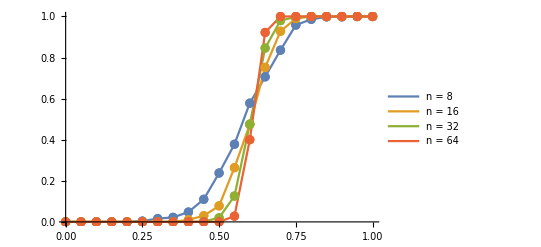

```mathematica
ListLinePlot[
{data1,data2,data3,data4},
DataRange->{0,1},Mesh->Full,
PlotLegends->{"n = 8","n = 16","n = 32","n = 64",}
]
```